Identification & Graph Structure of Rivers

DeFiglia, Christopher

Szudzik, Matthew

UNC Chapel Hill

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: The goal of the project was to identify rivers on maps and satellite images, and to calculate each river’s graph structure.

SUMMARY OF WORK: We implemented a function which uses street maps to highlight bodies of water on satellite images.  We also implemented a function to calculate the graph structure of the rivers at any given location.

RESULTS AND FUTURE  WORK: We would like to implement a random river generation function, and to identify rivers from satellite photos using a neural network. To improve the quality of highlighting/graphs, we would like to remove signs from street maps using a feature in Mathematica 11.2.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

◼ Hi! I’m Chris DeFiglia and my project was to identify rivers on maps and satellite images, and to calculate each river’s graph structure.
I ended up making two main functions, the first takes a location entity and spits out the satellite image of that location with the water highlighted.
 *Ask for an audience suggestion and show it as an example* (If this example isn’t a good one for graphs, then show a previously picked one.) 

◼ The second function also takes a given location entity but instead calculates the graph structure of the water at that location. Rivers appear long and winding while oceans and lakes look like webs. *Use the previous example to demonstrate the function*

◼ If you look closely on either image, you’ll see that there seems to be random highlighting or isolated graph structures. These spots are actually due to the fact that these functions use a specific shade of blue to pick out the water in the related street map and some of the road signs contain a small amount of this color. The problem isn’t too serious most of the time, but it can be amplified for areas with many signs. This issue can be remedied in the future using a feature in Mathematica 11.2 which removes signs from the street map.

Thanks!

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

◼ The function waterboundary will return a highlighting of all water in the satellite image given a location entity. This is achieved by taking a street map image of the location, cutting out the light blue portions, using some image processing to prep the image, and then using the prepped image as a mask in order to highlight the satellite image in question.

◼ The second function, watergraph will return the graph structure of the water in the related street map image of a given location entity. This is done in a similar way to the first image, however the satellite tile is never needed and different image processing is used to obtain the graph. The end product really is a graph object, so one could play with it using Wolfram’s graph functionality to get some interesting results.

Code

```mathematica
waterboundary[entity_]:=Module[{streetmap,color,r,bluemap,mask,satmap},
streetmap=RemoveAlphaChannel@FirstCase[GeoGraphics[entity,GeoBackground->"StreetMap"],_Image,$Failed,Infinity];
satmap=ImageResize[RemoveAlphaChannel@FirstCase[GeoGraphics[entity,GeoBackground->"Satellite"],_Image,$Failed,Infinity],ImageDimensions[streetmap]];
color=Apply[List,ColorConvert[Interpreter["Color"]["RGB 158 197 226"],"RGB"]];
r=If[ImageColorSpace[streetmap]≠"RGB",
ColorConvert[streetmap,"RGB"],streetmap];
bluemap=SetAlphaChannel[r,Binarize[r,(Norm[#-color]<.15)&]];
mask=Closing[#,7]&@FillingTransform@Binarize@bluemap;
HighlightImage[satmap,{EdgeForm[{Red,AbsoluteThickness[1.5]}],FaceForm[{Red,Opacity[.2]}], mask}]
];
(* This function takes a location entity as an input and outputs the satellite image of that location with the water highlighted in red *)
```

```mathematica
watergraph[entity_]:=Module[{streetmap,color,r,bluemap,mask},
streetmap=RemoveAlphaChannel@FirstCase[GeoGraphics[entity,GeoBackground->"StreetMap"],_Image,$Failed,Infinity];
color=Apply[List,ColorConvert[Interpreter["Color"]["RGB 158 197 226"],"RGB"]];
r=If[ImageColorSpace[streetmap]≠"RGB",
ColorConvert[streetmap,"RGB"],streetmap];
bluemap=SetAlphaChannel[r,Binarize[r,(Norm[#-color]<.15)&]];
mask=Closing[#,7]&@FillingTransform@Binarize@bluemap;
MorphologicalGraph@SkeletonTransform[mask]
];
(* This function takes a location entity as an input and outputs the graph structure of the water in the related street map image *)
```

The Initial Approach

◼ Since one of the primary goals of the project was to identify whether or not an image contained a river, we did make an attempt at it. We tried to first cut up the satellite images, binarize them, and then sort the tiny images based on the percentage of black and white pixels. We did this because in a large number of the initial images we saw, the water was usually much darker than the surrounding area. However as we looked at more test cases, this method of classifying images became obsolete. Many pictures require different binarize thresholds, some rivers are actually lighter than their surroundings, rivers may be indistinguishable from the background, cloud coverage either blocks the water or can even create dark spots on its own via shadows, rivers may appear too thin to be recognized as such, and the list goes on. As the list of issues grew, we decided to use the street map for the sole reason that they were reliable. The street maps may have roadsigns and gaps due to roads, but these issues can be largely solved or overlooked with basic image processing.

```mathematica
bwimagesplit[image_,threshold_:.5,pixelsize_:64]:=ImagePartition[#,pixelsize]&@(Binarize[#,threshold]&@image);
(* bwimagesplit splits up a satellite image into an array of images and binarizes it*)

bwpercent[bwimage_]:={N@((Flatten@ImageLevels[bwimage])[[ 2]]/(Times@@ImageDimensions@bwimage)),N@((Flatten@ImageLevels[bwimage])[[ 4]]/(Times@@ImageDimensions@bwimage))};
(* bwpercent finds the percent of black pixels and white pixels for a black/white image *)

riverbwsorter[nameimageassoc_,percent_]:=Module[{valueimagelist,river,notriver},
valueimagelist=Transpose[{(Part[#,2]&/@bwpercent/@Flatten[bwimagesplit/@Values[nameimageassoc]]),Flatten[bwimagesplit/@Values[nameimageassoc]]}];
river={};
notriver={};
If[#[[1]]≥percent,AppendTo[river,#[[2]]],AppendTo[notriver,#[[2]]]]&/@ valueimagelist;
Return[{river,notriver}]
]
(* riverbwsorter takes a location_name -> satellite_image association list, binarizes it, cuts it up, and then sorts the smaller images into "river" and "notriver" based
   on the percentage of white pixels in the image *)
```

Conclusions in Detail

◼ The function to remove street signs is highly needed as the shade of blue used in some of them interferes with the two water functions. As a result of its absence in Mathematica 11.1.1, various spots on the satellite image are unintentionally highlighted and the graphs can be slightly distorted. The significance of this issue increases with the number of roads and if the zoom level is low.
◼ The functions take a long time to evaluate. Using Seoul as an example, waterboundary takes roughly 2.3 seconds to evaluate and watergraph takes about 2.5 seconds.
◼ I would have liked to train an unsupervised neural network to generate river-like graphs but due to my inexperience and Mathematica’s lack of support (for now), this didn’t happen.

All Visualizations

#### Seoul, South Korea

```mathematica
-Graphics--Graphics--Graphics-
```

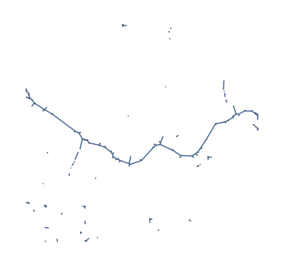
```mathematica
-Graphics--Graphics--Graphics-
```

Future Directions

◼ Find a way to accurately automate the classification of satellite images as: “river” or “not river” to make a training set. If this is accomplished, then you can probably train a neural network to identify rivers from satellite images. (This was the original goal of the project)

◼ Identify the name of a body of water based on a satellite image.

◼ Build a function that would generate a random river graph plot. This could be achieved by either training a neural network on graph plots or by implementing and already existing model.

Keywords

Geography

Image Processing

Graphs

Date

Last Modified: Tuesday, July 04, 2017

```mathematica
"Add Timestamp"
```